## File Information

```mathematica
(*Clear all values*) 
ClearAll["`*"]

(*Set Directory*)
dir=SetDirectory[NotebookDirectory[]];

(*Check what file is imported*)
files=FileNames["*.csv"]
parameterfiles="fitparameter.csv"

(*Sorting File Numbers*)
files2=StringDrop[#,0]&/@files;
files3=StringDrop[#,-6]&/@files2;
files4=ToExpression[#]&/@files3;
files5=Sort[files4];

(*Reconstruct File Names*)
files6=ToString[#]&/@files5;
files7=StringJoin["",#,"_1.csv"]&/@files6
files8=files7[[1;;7]]
```

{0_1.csv,15_1.csv,30_1.csv,45_1.csv,60_1.csv,75_1.csv,90_1.csv,fitparameter.csv}

fitparameter.csv

{0_1.csv,15_1.csv,30_1.csv,45_1.csv,60_1.csv,75_1.csv,90_1.csv,fitparamet_1.csv}

{0_1.csv,15_1.csv,30_1.csv,45_1.csv,60_1.csv,75_1.csv,90_1.csv}

## Result Data

```mathematica
(*Data Construction*)
(*Import files*)
rawdata=Import[#]&/@files8;
FileNo=Length[files8];

(*WN is array of wavenumber, SampleAVG is array of averaged sample, SamRefAVG is array of averaged sample / averaged refenence, Index is array of index for global fit*)
WN=rawdata[[All,All,1]];
Sampleraw=rawdata[[All,All,2]];
Fitraw=rawdata[[All,All,4]];
Index=Table[i,{i,0,FileNo 15,15},{j,1,Length[rawdata[[1]]]}];
```

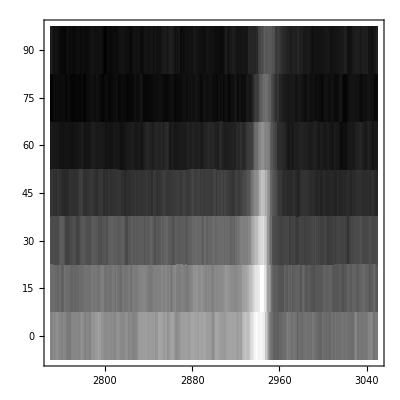
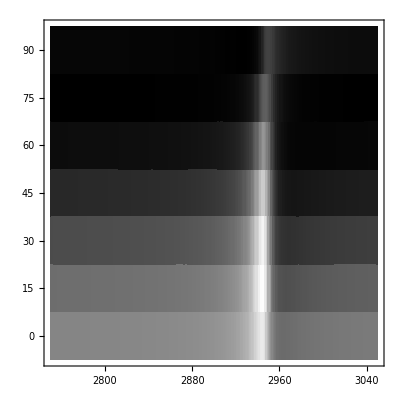

```mathematica
(*Reconstruct Data Table*)
Sample=Partition[Flatten[
Table[Drop[Transpose[Join[{WN[[i]]},{Index[[i]]},{Sampleraw[[i]]}]],{1}],{i,1,FileNo}]
],3];
Fited=Partition[Flatten[
Table[Drop[Transpose[Join[{WN[[i]]},{Index[[i]]},{Fitraw[[i]]}]],{1}],{i,1,FileNo}]
],3];

{{ListDensityPlot[Sample,InterpolationOrder->0, ColorFunction->GrayLevel,PlotRange->{{2750,3050},{-7.5,97.5}}],ListDensityPlot[Fited,InterpolationOrder->0, ColorFunction->GrayLevel,PlotRange->{{2750,3050},{-7.5,97.5}}]}}
```

## Fitting Model

```mathematica
sfg=Abs[(a1 (γ Sin[σ]+Cos[σ]))/(w-w1+ⅈ f1)+(n1(γn Sin[σ]+Cos[σ])) ⅇ^(-ⅈ p)]^2+n;
variable={a1,γ,f1,w1,n,n1,γn,p};
```

## Result Parameters

```mathematica
(*Data Construction*)
(*Import files*)
rawparameter=Import[parameterfiles];
%//MatrixForm
```

( | Estimate | Standard Error | tâ.80.90Statistic | Pâ.80.90Value
a1 | 3.25233 | 0.0801625 | 40.5717 | 5.47316×10^-266
Î.b3 | 1.76538 | 0.0562668 | 31.3752 | 2.00929×10^-177
f1 | 7.5019 | 0.138693 | 54.0901 | 8.60878967929×10^-400
w1 | 2947.18 | 0.135149 | 21806.9 | 1.60991733215×10^-5605
n | 0.363468 | 0.00225566 | 161.136 | 8.2589332079×10^-1182
n1 | -0.994619 | 0.00261358 | -380.558 | 6.24656394685×10^-1934
Î.b3n | -0.251329 | 0.00377965 | -66.4952 | 2.37591428111×10^-518
p | -0.553185 | 0.0192882 | -28.68 | 7.63566×10^-153
R^2 | 0.99285 | 0 | fitting target? | SamRefAVG)

## Result Data

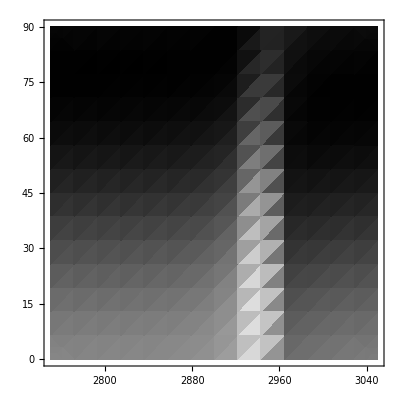

```mathematica
ToString[#]&/@variable;
StringInsert[%,"→",-1];
Table[StringJoin[%[[i]],ToString[rawparameter[[i+1,2]]]],{i,1,Length[variable]}];
results=ToExpression[#]&/@%;
SFG=sfg/.results;
DensityPlot[SFG/.σ->deg °,{w,2750,3050},{deg,0 ,90 },ColorFunction->GrayLevel]
Manipulate[Plot[SFG/.σ->deg °,{w,2750,3050},PlotRange->{0,3}],{deg,0 ,180 }]
```

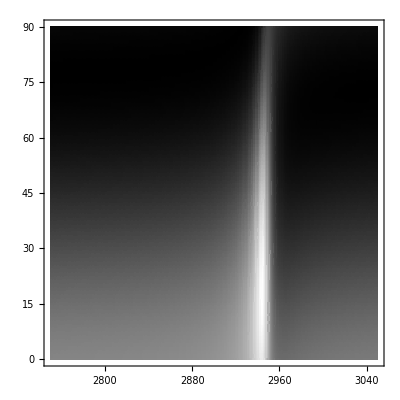

```mathematica
ListDensityPlot[Partition[Flatten[Table[{w,deg,SFG/.σ->deg °},{w,2750,3050},{deg,0 ,90 }]],3],ColorFunction->GrayLevel,InterpolationOrder->0]
```